```mathematica
ClearAll["Global`*"]

"LPlanar"

runNames= {"hawk_moth","buckeye_butterfly"};
paramterTypes={"l-conformal","l-elastic","l-uniform"};

figDir =FileNameJoin[{ParentDirectory[NotebookDirectory[]], "Figures"}];


(*runIndx =1; paramIndex =2;*)
spatialDim = 2;

numTimeSteps = 30; timeSteps = Range[numTimeSteps] -1;

colorTheme = "GreenPinkTones";




plotDefArrows[ runIndx_, paramIndex_, isSmoothing_:True][timeIndex_]:= (

arrowScale =  0.04; arrowThickness = 0.002; pointSize = 0.01;



paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
meshDir0 = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName}];

meshDir = FileNameJoin[{meshDir0, "time" <> ToString[timeIndex]}];

SetDirectory[meshDir0];

landmarkInds =Flatten[ Round[Import["landmarks.csv"]]] + 1;


 SetDirectory[meshDir];
(*initVerts = Import["vertices.csv"];
verts = Append[#,0]&/@Transpose[Transpose[initVerts] - Mean[initVerts]];*)

faces = Round[Import["faces.csv"]] + 1;
numFaces = Dimensions[faces][[1]];


If[isSmoothing,gaussianFilter = Import["GaussianFilter.csv"];
filter=gaussianFilter, filter =IdentityMatrix[numFaces] ];


SetDirectory[resultDir];
newVerts = Import["new_verts_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];
verts = Append[#,0]&/@newVerts;
(*allMax =Import[paramterType <>"_MaxDilations.csv"][[1,1]];*)
maxDims =Append[Import["MaxDimensions.csv"]//Flatten,0];


strainsRaw = Import["strains_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];

strains =  ArrayReshape[strainsRaw, {numFaces,spatialDim,spatialDim}];

{λ1,λ2} = Transpose[Eigenvalues/@strains];

eigVecs = (Append[#,0]&/@((Eigenvectors /@  strains)[[;;,1]]));

dils = filter.(λ1 + λ2);

shrs = filter.Abs[λ1 - λ2];

allMaxD = Max[Abs[dils]];
allMaxS = Max[shrs];

allMax = Max[allMaxS, allMaxD];


shears=  shrs/allMax;

dilations =0.5 (1 + dils/allMax);

shearVecs = eigVecs*shears*arrowScale;


dilationTri[i_]:= {ColorData[colorTheme][dilations[[i]]],Triangle[verts[[faces[[i]]]]]};
dilationTris = dilationTri /@ Range[numFaces];

centroids = Mean /@ (verts[[#]]&/@ faces);
arrows = Line[{centroids[[#]] - shearVecs[[#]],centroids[[#]] + shearVecs[[#]] }&/@Range[numFaces]];


landMarkVerts = verts[[landmarkInds]];


plotRegion = Cuboid[-1.2/2 maxDims,1.2/2 maxDims];

g1 = Graphics3D[{EdgeForm[None], dilationTris,Yellow, Thickness[arrowThickness],arrows,Red, PointSize[pointSize],Point[landMarkVerts], White, Opacity[0],plotRegion}, PlotRange->All, AspectRatio->Automatic, Boxed->False,ViewPoint->Top(*, PlotLabel->"Dilation_" <>runName <> "_time" <> ToString[timeIndex]*)]


)


plotDisplacementVecs[ runIndx_, paramIndex_][timeIndex_]:= (
arrowScale =  0.03; arrowThickness = 0.002;

paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName, "time" <> ToString[timeIndex]}];


 SetDirectory[meshDir];
initVerts2D = Import["vertices.csv"];
initVerts = Append[#,0]&/@Transpose[Transpose[initVerts2D] - Mean[initVerts2D]];

faces = Round[Import["faces.csv"]] + 1;
numFaces = Dimensions[faces][[1]];


SetDirectory[resultDir];
newVerts2D = Import["new_verts_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];
newVerts = Append[#,0]&/@Transpose[Transpose[newVerts2D] - Mean[initVerts2D]];

(*allMax =Import[paramterType <>"_MaxDilations.csv"][[1,1]];*)
maxDims =Append[Import["MaxDimensions.csv"]//Flatten,0];


arrows = Arrow[{initVerts,newVerts}//Transpose];

triangles = Triangle[initVerts[[#]]]&/@faces;


plotRegion = Cuboid[-1.2/2 maxDims,1.2/2 maxDims];

g1 = Graphics3D[{ EdgeForm[None],triangles,Blue, Arrowheads[0.005],Thickness[arrowThickness],arrows, White, Opacity[0],plotRegion}, PlotRange->All, AspectRatio->Automatic, Boxed->False,ViewPoint->Top]


)

fs = 19;smoothing =0.75;
getMaxDeformations[ runIndx_, paramIndex_][timeIndex_]:=(
paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
SetDirectory[resultDir];

strainsRaw = Import["strains_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];
numFaces = Length[strainsRaw];

strainRates =  ArrayReshape[ strainsRaw, {numFaces,spatialDim,spatialDim}];

{λ1,λ2} = Transpose[Eigenvalues/@strainRates];


Max/@{Abs[λ1+ λ2],Abs[λ1- λ2]}
)


plotMaxDeformations[ runIndx_, paramIndex_]:= (
smoothing =0.75;

{maxD, maxS} = LowpassFilter[#, smoothing]&/@Transpose[getMaxDeformations[ runIndx, paramIndex] /@ timeSteps];

times  = timeSteps/(numTimeSteps - 1.0);

label = Directive[FontFamily->"Myriad Pro", Black(*, FontSize->fs*) ];

ListLinePlot[{Transpose[{times, maxD}], Transpose[{times, maxS}]} , PlotStyle->{{Thick,Green},{Thick, Orange}}, PlotRange->All, PlotTheme->"SolidGrid", LabelStyle->label]
)



getMeanDeformations[ runIndx_, paramIndex_][timeIndex_]:=(
paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
SetDirectory[resultDir];

strainsRaw = Import["strains_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];
numFaces = Length[strainsRaw];

strainRates =  ArrayReshape[ strainsRaw, {numFaces,spatialDim,spatialDim}];

{λ1,λ2} = Transpose[Eigenvalues/@strainRates];

Mean/@{Abs[λ1+ λ2],Abs[λ1- λ2]}
)


plotMeanDeformations[ runIndx_, paramIndex_]:= (
smoothing =0.75;

{meanD, meanS} = LowpassFilter[#, smoothing]&/@Transpose[getMeanDeformations[ runIndx, paramIndex] /@ timeSteps];

times  = timeSteps/(numTimeSteps - 1.0);

label = Directive[FontFamily->"Myriad Pro", Black(*, FontSize->fs *)];

ListLinePlot[{Transpose[{times, meanD}], Transpose[{times, meanS}]} , PlotStyle->{{Thick,Green},{Thick, Orange}}, PlotRange->All, PlotTheme->"SolidGrid", LabelStyle->label]
)


plotMeanMaxDefs[ runIndx_, paramIndex_]:= (

{maxD, maxS} = LowpassFilter[#, smoothing]&/@Transpose[getMaxDeformations[ runIndx, paramIndex] /@ timeSteps];
{meanD, meanS} = LowpassFilter[#, smoothing]&/@Transpose[getMeanDeformations[ runIndx, paramIndex] /@ timeSteps];


times  = timeSteps/numTimeSteps;

label = Directive[FontFamily->"Myriad Pro", Black(*, FontSize->fs *)];


ListLinePlot[{Transpose[{times, maxD}], Transpose[{times, maxS}], Transpose[{times, meanD}], Transpose[{times, meanS}]} , PlotStyle->{{Thick,Green},{Thick, Orange}, {Thick,Green, Dashed},{Thick, Orange, Dashed}}, LabelStyle->label, MultiaxisArrangement->{{1, 2},{3,4}}]

)


compareBoundaries[ runIndx_, paramIndex_][timeIndex_]:= (

paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName, "time" <> ToString[timeIndex]}];

 SetDirectory[meshDir];
initVerts = Import["vertices.csv"];
deformedVerts = Import["vertices_deformed.csv"];

normals = Import["normal.csv"];
boundaryIndx = (Import["boundary_indices.csv"] + 1)//Flatten;

faces = Round[Import["faces.csv"]] + 1;

SetDirectory[resultDir];
newVerts = Import["new_verts_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];

(*arrows = Arrow[{deformedVerts[[boundaryIndx]], deformedVerts[[boundaryIndx]] + normals}//Transpose];
*)
(*{Graphics[{EdgeForm[Thickness[0.001]],Pink,Triangle[ newVerts[[#]]& /@ faces], Blue,Triangle[deformedVerts[[#]]&/@ faces],Red,arrows}, AspectRatio->Automatic],
Graphics[{ EdgeForm[Thickness[0.001]],Blue,Triangle[deformedVerts[[#]]&/@ faces],Pink,Triangle[ newVerts[[#]]& /@ faces],Red(*, arrows*)}, AspectRatio->Automatic]}*)

Graphics[{Red,Point[ newVerts], Blue,Point[ deformedVerts], Orange, Point[initVerts]}, AspectRatio->Automatic]
)
```

LPlanar

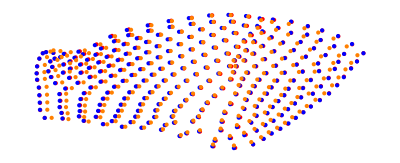

```mathematica
runIndx =1; paramIndx =2; timeIndx =15;
compareBoundaries[runIndx, paramIndx][timeIndx]
```

```mathematica
runIndx =2; 

(*maxPlots = plotMaxDeformations[runIndx, #]&/@Range[Length[paramterTypes]];
meanPlots = plotMeanDeformations[runIndx, #]&/@Range[Length[paramterTypes]];*)
meanMaxPlots = plotMeanMaxDefs[runIndx, #]&/@Range[Length[paramterTypes]]


arrowPlots[tIndx_]:= plotDefArrows[runIndx, #][tIndx]&/@ Range[Length[paramterTypes]];
gRowStrain = GraphicsRow[(GraphicsColumn [ arrowPlots[#]])&/@  {1,15, 29}]


SetDirectory[figDir];

(*Export[runNames[[runIndx]]  <> "_maxDeformation.pdf", maxPlots, ImageResolution->1000];
Export[runNames[[runIndx]]  <> "_meanDeformation.pdf", meanPlots, ImageResolution->1000];*)

Export[runNames[[runIndx]]  <> "_LmeanMaxDeformation.pdf", meanMaxPlots, ImageResolution->1000];

Export[runNames[[runIndx]]  <> "_Lstrain.pdf", gRowStrain, ImageResolution->3000];
```

{-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
{plotDefArrows[1,1][15],plotDefArrows[1,2][15], plotDefArrows[1,3][15]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListAnimate[plotDefArrows[1,1]/@timeSteps]
```

```mathematica
ListAnimate[plotDisplacementVecs[1,1]/@timeSteps]
```

```mathematica
ListAnimate[plotDefArrows[1,3]/@timeSteps]
```